```mathematica
<<Dzhanybekhov`
```

```mathematica
ClearAll[e1,e2,e3,o,g];
e1={1,0,0};e2={0,1,0};e3={0,0,1};
o={0,0,0};g=1.25;
```

```mathematica
ClearAll[apparatus];
apparatus[rq_]:=
With[{r1=0.125,r2=0.25,r3=0.0625},
Module[{angle,direction},
{angle,direction}=θvrq[rq]
;Rotate[{
Lighter[Red,0.50],Sphere[e1,r1]
,Lighter[Purple,0.50],Sphere[-1e1,r1] 
,Lighter[Green,0.50],Sphere[e2,r2]
,Lighter[Yellow,0.50],Sphere[-1e2,r2]
,RGBColor[1,.71,0],Opacity[0.125]
,Cylinder[{-e3,e3}/10000]
},angle,direction]]];
```

```mathematica
ClearAll[showApparatus];
showApparatus[ωb_,Lb_,ωs_,Ls_,rq_]:=
Show[{
Graphics3D[{
Magenta,Arrow[Tube[{o,Ls},0.02]]
,Red,Arrow[Tube[{o,Lb},0.02]]
,Cyan,Arrow[Tube[{o,ωs/10},0.02]]
,Blue,Arrow[Tube[{o,ωb/10},0.02]]
,White
,apparatus[rq]}]}
,Axes->True
,PlotRange->{{-g,g},{-g,g},{-g,g}}
,AxesLabel->{"X","Y","Z"}
,ImageSize->Large
];
```

```mathematica
DynamicModule[
{t=0
,dt=0.03/4
,ωb={6,.1,0}
,ωs=0
,rq=rq[π/4.,{0,1.,0}]
,M=0.0801587/2
,m=0.0825397/2
,mm=0.00396825
,Ib
,Ibi
,Lb
,Ls
}
,Ib=DiagonalMatrix[{2M,2m,mm}]
;Ibi=Inverse@Ib
;Dynamic[
t+=dt
;rq=rqn[rq,ωb,dt]
;ωb=ωn[ωb,Ib,Ibi,dt]
;ωs=vq[rq**qv[ωb]**rq*]//Chop
;Lb=Ib.ωb
;Ls=vq[rq**qv[Lb]**rq*]//Chop
;showApparatus[ωb,Lb,ωs,Ls,rq]]]
```

```mathematica
ClearAll[results];
results[nPoints_,ωb0_,rq0_,Ib_,dt_]:=
Module[{Lbtm1,rqtm1,ωbtm1,Lbt,Lst,ωbt,ωst,rqt,Ibi}
,ωbt=ωb0
;rqt=rq0
;Ibi=Inverse@Ib
;Table[
rqtm1=rqt
;ωbtm1=ωbt
;rqt=rqn[rqtm1,ωbtm1,dt]
;ωbt=ωn[ωbtm1,Ib,Ibi,dt]
;Lbt=Ib.ωbt
(*;Lbtm1=Lbt*)
(*;Lbt=LbnRK[Lbtm1,ωbtm1,rqt,dt]*)
;Lst=vq[rqt**qv[Lbt]**rqt*]//Chop
;ωst=vq[rqt**qv[ωbt]**rqt*]//Chop
;{ωbt,Lbt,ωst,Lst,rqt}
,{t,0,nPoints dt,dt}]];
```

```mathematica
ClearAll[experiment];
Options[experiment]=
{ωb0->{6,.1,0}
,rq0->rq[π/4.0,{0,1,0}]
,n->3000
,M->0.0801587/2
,m->0.0825397/2
,mm->0.00396825
,dt->0.03/4};
experiment[OptionsPattern[]]:=
experiment[
OptionValue@ωb0
,OptionValue@rq0
,OptionValue@n
,DiagonalMatrix[
{2OptionValue@M
,2OptionValue@m
,OptionValue@mm}]
,OptionValue@dt];
experiment[ωb0_,rq0_,nPointsInput_,Ib_,dt_]:=
(integrant=
results[
nPoints=nPointsInput
,ωb0,rq0,Ib,dt];);
```

```mathematica
experiment[ωb0->{6,0.1,0},dt->0.03/8];
```

```mathematica
ClearAll[getLb,getωb,getωs,getLs,getwq,getrq];
getLb[integrant_]:=Transpose[integrant]⟦2⟧;
getLs[integrant_]:=Transpose[integrant]⟦4⟧;
getωb[integrant_]:=Transpose[integrant]⟦1⟧;
getωs[integrant_]:=Transpose[integrant]⟦3⟧;
getrq[integrant_]:=Transpose[integrant]⟦5⟧;
getwq[integrant_]:=wrq/@Transpose[integrant]⟦5⟧;
```

### Angular Momentum: Body Frame

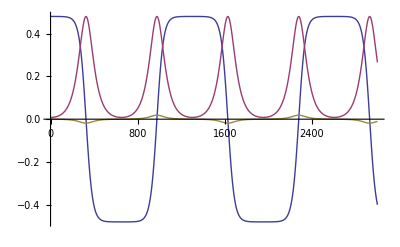

```mathematica
ListLinePlot[Transpose@getLb[integrant]]
```

### Angular Momentum: Space Frame

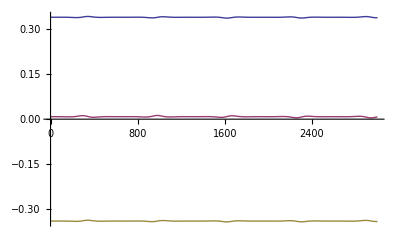

```mathematica
ListLinePlot[Transpose@getLs[integrant]]
```

### Angular Velocity: Space Frame

What about the angular velocity in the space frame? Is it constant? No, and this is the origin of the effect. We can see that it’s going to flip and wobble, but periodically:

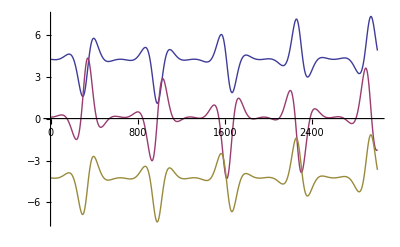

```mathematica
ListLinePlot[Transpose@getωs[integrant]]
```

### Angular Velocity: Body Frame

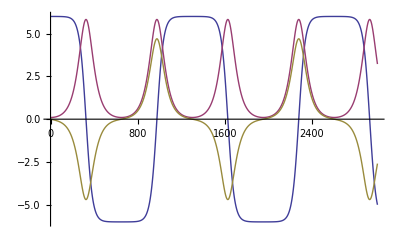

```mathematica
ListLinePlot[Transpose@getωb[integrant]]
```

### Rotation Quaternion

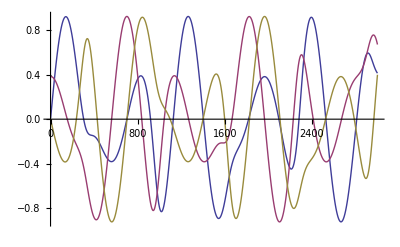

```mathematica
ListLinePlot[Transpose@(vq/@getrq[integrant])]
```